```mathematica
fun1=x1^2-3 x2^2+2+t;
fun2=x1 x2-1+7t;
```

```mathematica
D[fun1,x2]*D[fun2,t]-D[fun2,x2]*D[fun1,t]
```

-x1-42 x2

```mathematica
Clear[fun1,fun2];
```

```mathematica
fun1[t_,x1_,x2_]:=x1^2-3 x2^2+2+t;
fun2[t_,x1_,x2_]:=x1 x2-1+7t;
```

```mathematica
1/0.0000001^2((fun1[0,1,1+0.0000001]-fun1[0,1,1])(fun2[0+0.0000001,1,1]-fun2[0,1,1])-(fun2[0,1,1+0.0000001]-fun2[0,1,1])(fun1[0+0.0000001,1,1]-fun1[0,1,1]))
```

-43.

```mathematica
FindRoot[2*x-4+Sin[2*Pi*x],{x,2}]
```

{x→2.}

```mathematica
D[(-4+2 x+Sin[2 π x]), x]
```

2+2 π Cos[2 π x]

```mathematica
data=Import["/Users/zdeng/Dropbox/git/test_by_CLion_2/cmake-build-debug/sol.dat"];
```

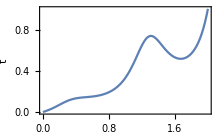

```mathematica
t=Transpose[data][[4]];
x=Transpose[data][[3]];
ListLinePlot[Transpose[{x,t}],
Frame->True,
ImageSize->{220,Automatic},
FrameLabel->{{HoldForm[t],None},{HoldForm[x],None}},PlotLabel->None,LabelStyle->{FontFamily->"Palatino",9,GrayLevel[0]}]
```

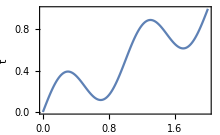

```mathematica
t=Transpose[data][[4]];
x=Transpose[data][[3]];
ListLinePlot[Transpose[{x,t}],
Frame->True,
ImageSize->{220,Automatic},
FrameLabel->{{HoldForm[t],None},{HoldForm[x],None}},PlotLabel->None,LabelStyle->{FontFamily->"Palatino",9,GrayLevel[0]}]
```